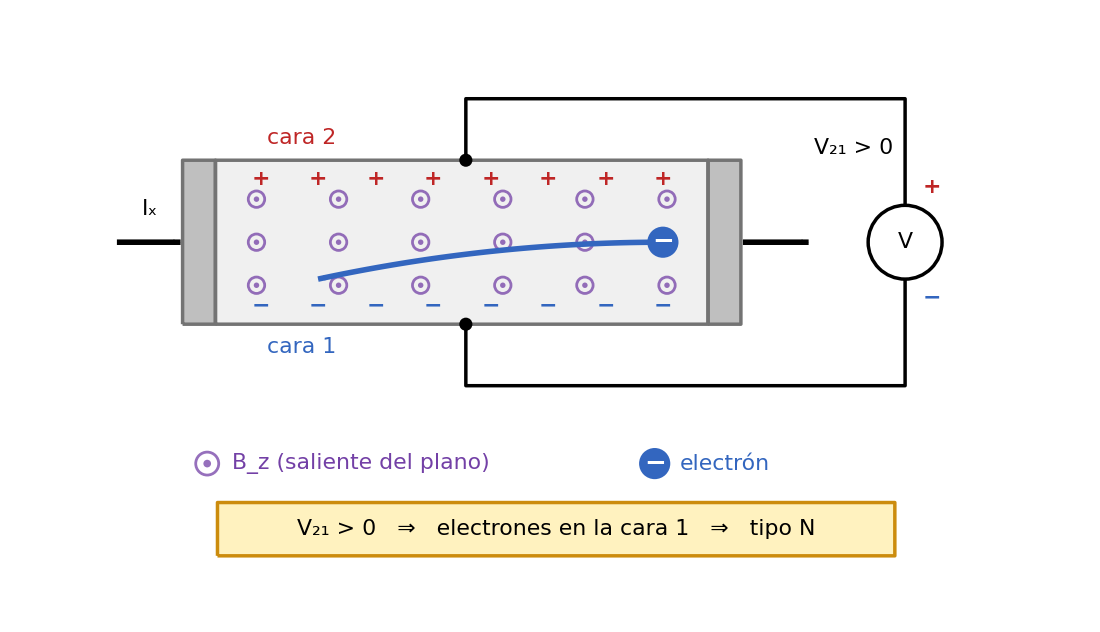

```mathematica
diagramaHall = Module[
  {fs, cAzulB, cRojo, cVio, cGris, cOro, cOroB,
   ins, insI, insD, flecha, caja, electron, bmag, trayec},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;   (* tamaño de fuente único para todo el gráfico *)
  cAzulB = RGBColor[0.20, 0.40, 0.75];  cRojo = RGBColor[0.75, 0.15, 0.15];
  cVio   = RGBColor[0.45, 0.25, 0.65];  cGris = GrayLevel[0.45];
  cOro   = RGBColor[1.0, 0.95, 0.75];   cOroB = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  flecha[p1_, p2_, col_] :=
    {col, AbsoluteThickness[4], Arrowheads[0.025], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  electron[pos_] :=
    {cAzulB, Disk[pos, 0.38],
     Text[Style["−", Round[1.2 fs], Bold, White], pos]};
  bmag[pos_, r_: 0.2] :=
    {Opacity[0.75, cVio], AbsoluteThickness[2], Circle[pos, r], Disk[pos, r/3]};

  (* trayectoria del electrón: se mueve hacia -x y se desvía hacia la cara 1 *)
  trayec = Table[{x, 4.0 - 0.9 ((13.4 - x)/8.4)^2}, {x, 13.4, 5.0, -0.2}];

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* barra semiconductora y contactos de corriente *)
    {GrayLevel[0.94], EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{2.5, 2}, {14.5, 6}]},
    {GrayLevel[0.75], EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{1.7, 2}, {2.5, 6}], Rectangle[{14.5, 2}, {15.3, 6}]},

    (* corriente longitudinal *)
    flecha[{0.1, 4}, {1.65, 4}, Black],
    ins[Row[{Subscript["I", "x"]}], {0.9, 4.8}],
    flecha[{15.35, 4}, {16.95, 4}, Black],

    (* campo magnético saliente del plano *)
    Table[bmag[{x, y}], {x, 3.5, 13.5, 2.0}, {y, {2.95, 4.0, 5.05}}],

    (* acumulación de carga en las caras: + en la cara 2, - en la cara 1 *)
    Table[Text[Style["+", fs, Bold, cRojo], {x, 5.55}], {x, 3.6, 13.4, 1.4}],
    Table[Text[Style["−", fs, Bold, cAzulB], {x, 2.45}], {x, 3.6, 13.4, 1.4}],
    ins["cara 2", {4.6, 6.55}, cRojo],
    ins["cara 1", {4.6, 1.45}, cAzulB],

    (* electrón desviado hacia la cara 1 *)
    {cAzulB, AbsoluteThickness[4], Arrowheads[0.025], Arrow[trayec]},
    electron[{13.4, 4.0}],

    (* contactos Hall y voltímetro *)
    {Black, AbsoluteThickness[2.5],
     Line[{{8.6, 6}, {8.6, 7.5}, {19.3, 7.5}, {19.3, 4.9}}],
     Line[{{8.6, 2}, {8.6, 0.5}, {19.3, 0.5}, {19.3, 3.1}}]},
    {Black, Disk[{8.6, 6}, 0.16], Disk[{8.6, 2}, 0.16]},
    {EdgeForm[{AbsoluteThickness[2.5], Black}], White, Disk[{19.3, 4}, 0.9]},
    ins["V", {19.3, 4}],
    Text[Style["+", fs, Bold, cRojo], {19.95, 5.35}],
    Text[Style["−", fs, Bold, cAzulB], {19.95, 2.65}],
    insD[Row[{Subscript["V", "21"], " > 0"}], {19.0, 6.3}],

    (* leyenda *)
    bmag[{2.3, -1.4}, 0.28],
    insI[Row[{Subscript["B", "z"], " (saliente del plano)"}], {2.9, -1.4}, cVio],
    electron[{13.2, -1.4}],
    insI["electrón", {13.8, -1.4}, cAzulB],

    (* conclusión del apartado a) *)
    caja[{10.8, -3.0}, {16.5, 1.3}, cOro, cOroB],
    ins[Row[{Subscript["V", "21"], " > 0   ⇒   electrones en la cara 1   ⇒   tipo N"}],
     {10.8, -3.0}]
   },
   ImageSize -> 1100,
   PlotRange -> {{-0.3, 21.6}, {-4.1, 8.5}},
   PlotRangePadding -> None,
   AspectRatio -> 12.6/21.9,
   Background -> White]
];
diagramaHall
```